# Money

A short discussion on the circulation of money in a network

Leanne Ussher, Jun. 24,  2018

Money is not well understood. Most text books argue that it is based on trust and its value is determined by supply and demand. While this is true, they often omit to mention that money is constantly being created and destroyed by the entities that make money. The central banks, commercial banks, and federal government can all create and destroy fiat money. No other entities make or destroy the legal tender, money M1. However, the private creation of  complementary currency is possible. We show the structure of a the Berkshire’s complementary currency.

## Fiat Money

A common definition of fiat money is:

```mathematica
Entity["Word","fiat money"][EntityProperty["Word","Definitions"]]
```

{{fiat money,Noun}→money that the government declares to be legal tender although it cannot be converted into standard specie}

It seems strange to some that money can be created from nothing, but through the power of a government to impose usage through law and the power to  tax, fiat or sovereign money becomes stable and valuable.

Fiat Currency is an IOU (I owe you). This money is called M1, and it primarily consists of

1) federal notes (green backs) which are in circulation (outside of bank vaults); and

2) bank deposits.

In all cases this money is created from nothing,  the Federal reserve creates the former, while banks create the latter. Indeed as Hyman Minsky once said “anyone can create money; the problem is to get it accepted”.

A plot of the stock of money or M1 over time is below.

```mathematica
WolframAlpha["plot money supply m1",IncludePods->{"History:MoneySupply:EconomicData"}]
```

WolframAlphaQueryResults

## Velocity of Fiat Money

Each time money circulates (quantity of money times the number of transactions) it is in exchange for goods or services (price times quantity) we can write this as an equation:

M.V = P.Y

The circulation of money is easiest to understand in a closed network with just trade, and in this case we do not have a central bank or private banks. In the flow graph below there is a source at the top - the Government - that injects money into the system. And the same node (the Government) at the bottom that takes extinguishes currency from the system. The management of injection and extraction of money is done to keep the value of money stable.

In this case the Government injects 15 units of cash into the network. These 15 units can circulate around the network from node to node, and at each point the money is distributed or circulates through the system.  (source and sink are both the government). Infinite loops could occur, as shown, but we assume that these government departments decide only to trade with each other according to the parameters shown in the graph.

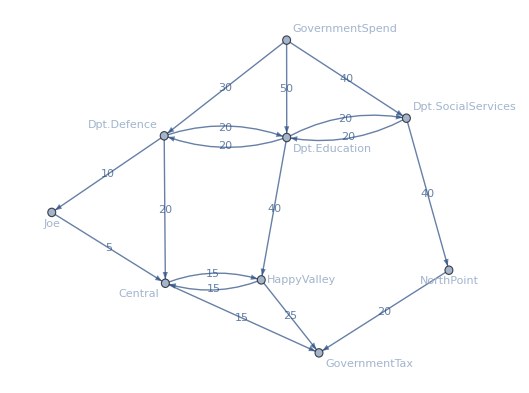

```mathematica
h
```

```mathematica
Total[PropertyValue[{h,#},EdgeCapacity]&/@EdgeList[h]]
```

405

In this case we have the following transactions, giving us a total number of transactions

Flows

Government Spending | 120
M.V | 405
Leakages | 60
Taxes | 60

In this simple network money is conserved or the stock of money remains constant when it is not being changed by the Government. The circulation of money MV creates income of PY. The money does not circulate more because there are some nodes in the network that also act as sinks and reduce velocity which is 3.375:

Leakages

Joe | 5
NorthPoint | 20
Happy Valley | 15
Dpt.Ed | 10
Central | 10

## A Local Currency

When there are leakages from a network, it may be warranted for a community to create a local currency. The local currency is usually not exchangeable into the national currency. As a result once the currency is issued it cannot leave through imports or foreign investment. Instead it stays in the community at a higher velocity. Below is a network of the Berkshare’s community currency, take from 3 days of trading.

Data

```mathematica
Code (* demonstrate a specific application *)
```

```mathematica
Import[NotebookDirectory[]<>"schumacher_data2.csv"]
```

```mathematica
Import[NotebookDirectory[]<>"schumacher_data2.csv"]
```

```mathematica
g=AdjacencyGraph[{{7,0,0,0,11,0,0,0,0,0,0,0,0,6,8,0,0,0,0,0,0,10,0,12,0,0,0,0,0,0,0,0,0,0,17,0,0,0,0,0,9,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,3,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,2,0,0,0,0,0,0,2,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,4,0,458,0,0,0,0,24,0,2,10,4,3,0,27,1,0,0,0,45,5,15,0,12,5,2,9,49,0,0,0,0,27,0,0,0,34,3,8,0,0,7,3,0,0,0},{0,1,0,0,1,15,0,0,0,3,0,0,0,9,4,2,7,3,0,0,0,6,0,15,0,0,15,8,4,4,0,0,0,0,28,1,0,2,1,4,8,1,1,1,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,2,2,0,0,5,7,0,4,2,91,6,0,7,3,0,0,0,6,1,55,0,1,0,0,0,11,0,0,0,0,23,0,0,0,12,0,1,2,0,11,0,0,0,0},{0,0,0,0,13,0,0,0,0,48,0,3,5,0,2,10,0,4,6,0,0,16,0,0,0,0,12,0,2,6,0,0,0,0,5,0,0,29,0,0,4,6,0,10,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,0,0,0,19,4,10,0,0,3,2,0,0,0,2,0,0,0,0,0,0,0,0,18,0,0,0,0,0,0,3,0,0,28,0,0,0,0,0,0,0},{0,0,0,0,7,0,0,1,1,0,0,40,42,9,0,0,2,0,0,0,0,2,0,2,0,0,0,0,0,0,0,0,0,0,2,2,0,1,0,1,0,3,0,0,0,0,0,0},{0,2,0,1,9,1,0,0,2,23,0,0,14,511,10,0,0,7,0,0,0,27,3,61,0,17,6,2,5,19,8,0,0,0,39,8,0,0,64,7,2,8,2,22,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,4,45,0,0,0,0,4,0,0,0,0,0,1,0,0,0,0,5,0,2,0,0,0,0,5,0,1,2,1,3,0,0,0},{0,0,4,0,0,3,0,2,0,1,0,0,4,3,1,0,6,24,0,0,0,3,2,2,0,2,5,0,0,3,0,0,1,0,8,0,0,3,4,0,3,2,2,3,2,0,3,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,4,0,0,16,0,18,0,0,1,0,12,0,0,2,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,8,0,0,0,0},{0,0,0,0,5,0,0,0,0,0,0,0,5,5,9,0,0,0,0,0,0,0,0,3,0,50,0,0,0,0,0,0,0,0,16,12,0,0,0,0,0,0,0,9,0,0,0,0},{0,0,7,0,3,0,0,1,0,0,0,0,19,0,104,0,7,1,0,0,0,6,0,37,0,0,5,0,0,9,0,0,0,0,3,0,0,0,0,8,0,1,0,0,0,2,0,0},{0,1,12,0,13,0,0,0,1,22,0,3,4,21,17,0,10,11,0,0,0,381,1,14,5,33,31,12,0,7,0,0,0,0,42,0,0,1,3,1,0,13,16,41,3,2,0,0},{0,2,0,0,28,0,0,0,0,22,0,8,3,7,16,0,9,6,0,2,0,25,10,0,0,2,12,0,21,17,21,0,6,0,12,0,0,43,0,7,0,7,0,31,4,5,0,0},{0,0,0,0,25,3,0,0,0,28,0,4,20,76,3,0,0,10,0,9,0,28,0,223,57,54,20,0,10,1,0,0,5,0,32,0,0,0,53,5,46,10,10,27,6,2,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,18,0,0,0,0,28,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,4,0,8,3,0,0,2,21,0,0,11,15,4,15,5,4,0,0,0,29,0,16,0,16,82,0,0,10,0,0,3,0,46,0,0,16,20,12,13,12,0,10,2,0,40,0},{0,0,4,0,0,0,0,0,1,0,0,1,10,19,0,2,2,3,0,0,0,11,0,6,0,0,5,48,0,2,0,0,0,0,12,0,0,6,0,1,20,3,0,12,0,0,1,0},{0,0,0,10,0,0,0,0,0,0,0,9,0,2,0,0,0,0,0,0,0,0,0,0,62,0,0,0,34,5,0,0,0,0,1,0,0,0,0,3,15,3,8,0,0,0,0,0},{4,3,1,0,0,1,0,0,8,5,0,0,12,6,7,0,3,3,0,8,1,12,1,0,0,5,3,0,0,17,0,1,4,0,13,9,0,0,1,5,15,4,0,1,2,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,3,0,9,1,0,3,0,2,0,0,9,20,6,0,0,1,0,0,0,8,0,2,0,2,11,0,0,6,0,5,0,0,22,0,0,0,0,0,2,0,0,7,2,0,0,0},{0,1,3,0,9,0,0,0,1,8,0,0,2,5,0,0,0,1,0,0,0,4,0,2,0,8,7,0,0,17,0,0,44,0,11,0,0,0,0,0,9,0,0,0,1,2,0,0},{0,11,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,19,0,98,14,0,0,2,45,0,23,43,37,23,0,0,16,25,22,1,127,8,48,37,32,51,9,25,29,20,0,19,0,1322,25,0,13,65,25,17,39,45,16,17,17,6,0},{0,0,0,0,6,0,0,0,0,2,0,0,12,0,0,0,7,0,0,0,0,0,0,2,0,11,0,0,0,0,0,0,0,0,5,3,0,0,0,0,18,5,7,17,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6,0,0,0,0,0},{0,1,0,0,36,0,0,0,5,36,0,123,7,28,17,0,7,1,0,0,0,26,1,8,16,94,19,6,3,24,19,0,0,0,39,5,0,5,404,12,3,10,0,15,6,6,3,0},{0,0,0,0,0,1,0,0,0,2,0,0,2,0,9,0,2,0,0,0,0,0,0,3,0,0,12,0,0,0,0,0,0,0,4,0,0,6,0,5,1,0,9,2,0,0,0,0},{0,0,0,0,0,0,0,5,0,5,0,0,0,23,3,0,0,9,0,0,0,10,0,0,0,14,10,0,0,0,5,0,1,0,58,0,0,21,0,0,114,1,11,7,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,14,0,4,5,0,0,2,0,0,0,0,0,26,0,0,2,0,0,0,0,0,0,0,0,0,0,0,1,5,0,56,0,4,0,0,0,0},{0,1,0,0,3,0,0,0,2,6,0,0,1,6,0,0,30,4,0,0,0,20,0,0,0,0,0,0,8,1,0,0,4,0,5,2,0,0,0,0,0,0,2,0,0,0,0,0},{0,0,0,0,10,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,26,0,0,0,0,0,0,0,0,15,0,0,0,6,0,3,0,3,3,0,11,0,0},{0,0,9,0,10,0,0,0,2,0,0,19,12,14,0,0,0,0,0,0,0,14,9,7,0,0,4,0,9,10,4,0,0,0,26,0,0,0,2,11,0,2,0,6,33,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,14,0,8,0,0,0,0,0,0,0,32,0,0,0,19,2,0,0,0,0,0,0,0,7,0,0,0,0,0,0,0,0,0,0,0,40,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}]
```

```mathematica
nameList=Flatten[Import[NotebookDirectory[]<>"schumacher_data_names.csv"]]
```

{Animal Presence,Baker's wife,Barrington Ballet,Beckwhith's Glass,Berkshire Child,Berkshire Coffee,Berkshire Craft,Berkshire Cupboard,Bill's Pharmacy,Byzantium,Cabinet Works,Caligari's,Captain Toss,Carr Bros HDWE,Castle St. Café,Harry Conklin,Crystal Essence,Daily Bread,decades,Diva,Dolby Florist,EverGreen,Farshaw's,Frames on Wheels,Galeria Arriba,Gans Appliance,Gatby's,Gorham & Norton,Harland Foster,Herbert's Shoes,Home Textures,Impoco's Video,Initially Yours,Inn at Green River,Jack's,Jillifers,Jodi's,Kahn's,Krol Jewelers,La Tomate,Lamplighter,Laramee Cleaners,Leatherwoods,Main st Clothing,Manhattan Pizza,Mamphis Hair,Mill River Studio,Monument Mt}

```mathematica
vertexNames=Flatten[Position[nameList,#]][[1]]->#&/@nameList
```

{1→Animal Presence,2→Baker's wife,3→Barrington Ballet,4→Beckwhith's Glass,5→Berkshire Child,6→Berkshire Coffee,7→Berkshire Craft,8→Berkshire Cupboard,9→Bill's Pharmacy,10→Byzantium,11→Cabinet Works,12→Caligari's,13→Captain Toss,14→Carr Bros HDWE,15→Castle St. Café,16→Harry Conklin,17→Crystal Essence,18→Daily Bread,19→decades,20→Diva,21→Dolby Florist,22→EverGreen,23→Farshaw's,24→Frames on Wheels,25→Galeria Arriba,26→Gans Appliance,27→Gatby's,28→Gorham & Norton,29→Harland Foster,30→Herbert's Shoes,31→Home Textures,32→Impoco's Video,33→Initially Yours,34→Inn at Green River,35→Jack's,36→Jillifers,37→Jodi's,38→Kahn's,39→Krol Jewelers,40→La Tomate,41→Lamplighter,42→Laramee Cleaners,43→Leatherwoods,44→Main st Clothing,45→Manhattan Pizza,46→Mamphis Hair,47→Mill River Studio,48→Monument Mt}

Graph of Berkshare community currency network

```mathematica
CommunityGraphPlot[SimpleGraph[g,VertexLabels->vertexNames]]
```

-Graphics-

## Author contact information

Leanne Ussher

ussher@gmail.com